Notebook Setup

```mathematica
Remove["Global`*"](*Clears all variables*)

SetOptions[EvaluationNotebook[],AutoStyleOptions->{"CommentStyle"->{FontColor->Blue,FontFamily->"Helvetica",FontSize->10,FontWeight->"Thin"}}]; (*Comments are set to be blue and thin*)

SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->18},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True]; (*Sets Plots to have a certain color scheme and to use a frame*)

SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->18},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,Joined->True,FrameTicks->{Automatic,Automatic},ImagePadding->{{70, 10}, {50, 10}}]; (*Sets ListPlots to have a certain color scheme and to use a frame*)
```

Physics Setup

```mathematica
μs=10^-6; (*Units*)
MHz=10^6;
GHz=10^9;
Ωs=2π 222 MHz; (*Stokes Rabi frequency*)
Ωp=2π 37 MHz; (*Pump Rabi frequency*)
Ωpp=√12 Ωp; (*Detuned pump Rabi frequency*)
Δp=2π 21 GHz;
Γ=2π 100 MHz; (*Scattering from intermediate states*)
tmax=20; (*Length of time, in μs, that the simulation runs for. Typically τ+w. *)
precision=10; (*Significant figures used for numerical simulations like NDSolve.*)
H[t_,Δs0_,Δs1_,Δs2_,w_]=({{0, 1/2 Ωp, 1/2 Ωpp, 0}, {1/2 Ωp, Δp-ⅈ Γ/2, 0, 1/2 Ωs}, {1/2 Ωpp, 0, Δp+2π 3.4 GHz-ⅈ Γ/2, 0}, {0, 1/2 Ωs, 0, Δp-(2π 21GHz+Δs0 MHz+Δs1 MHz^2 (t-w)+Δs2 MHz^3 (t-w)^2)}});
```

```mathematica
P[t_]={p1[t],p2[t],p3[t],p4[t]};
(*We define the population in each of the four bare basis states to be time dependent*)
init=P[0]=={1,0,0,0};(*We set the population to initially reside in the initial state*) 
SE=ⅈ P'[t]==H[t,Δs0,Δs1,Δs2,w].P[t];(*The Schrodinger equation*)
PSoln=ParametricNDSolve[{SE,init},{p1,p2,p3,p4},{t,0,10 μs},{Δs0,Δs1,Δs2,w},PrecisionGoal->7,Method->{"ParametricSensitivity"->None}];(*We solve the Schrodinger equation parametrically, such that we obtain numerical solutions for the four populations as a function of τ and w.*)
PSoln (*The module outputs the four time-dependent populations, which are functions of τ and w.*)
```

{p1→ParametricFunction[<>],p2→ParametricFunction[<>],p3→ParametricFunction[<>],p4→ParametricFunction[<>]}

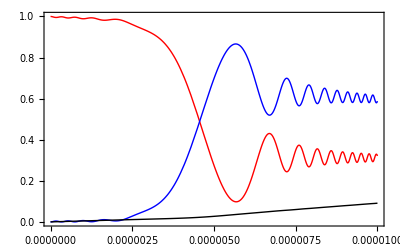

```mathematica
Plot[{Evaluate[Abs[p1[-2.535,1,1,5μs][t]]^2/.PSoln],Evaluate[Abs[p4[-2.535,1,1,5μs][t]]^2/.PSoln],Evaluate[1-Abs[p1[-2.535,1,1,5μs][t]]^2-Abs[p4[-2.535,1,1,5μs][t]]^2/.PSoln]},{t,0,10μs}]
```

```mathematica
tableTEST=Table[{ΔsTEST,Evaluate[Abs[p1[2π 21GHz-ΔsTEST][1μs]]^2/.PSoln]},{ΔsTEST,-10MHz,15MHz,0.5 MHz}]
```

{{-1.×10^7,0.995396},{-9.5×10^6,0.99484},{-9.×10^6,0.992989},{-8.5×10^6,0.989973},{-8.×10^6,0.986225},{-7.5×10^6,0.982428},{-7.×10^6,0.979395},{-6.5×10^6,0.977893},{-6.×10^6,0.978442},{-5.5×10^6,0.981136},{-5.×10^6,0.985503},{-4.5×10^6,0.990464},{-4.×10^6,0.9944},{-3.5×10^6,0.995325},{-3.×10^6,0.991164},{-2.5×10^6,0.980087},{-2.×10^6,0.960849},{-1.5×10^6,0.933083},{-1.×10^6,0.897492},{-500000.,0.855898},{0.,0.811118},{500000.,0.766698},{1.×10^6,0.726509},{1.5×10^6,0.69428},{2.×10^6,0.673125},{2.5×10^6,0.665138},{3.×10^6,0.671114},{3.5×10^6,0.690444},{4.×10^6,0.7212},{4.5×10^6,0.760384},{5.×10^6,0.804326},{5.5×10^6,0.849151},{6.×10^6,0.891248},{6.5×10^6,0.927687},{7.×10^6,0.956507},{7.5×10^6,0.976856},{8.×10^6,0.988966},{8.5×10^6,0.993977},{9.×10^6,0.993658},{9.5×10^6,0.990065},{1.×10^7,0.985206},{1.05×10^7,0.980758},{1.1×10^7,0.977871},{1.15×10^7,0.977092},{1.2×10^7,0.978395},{1.25×10^7,0.981306},{1.3×10^7,0.985078},{1.35×10^7,0.988898},{1.4×10^7,0.992058},{1.45×10^7,0.99409},{1.5×10^7,0.994826}}

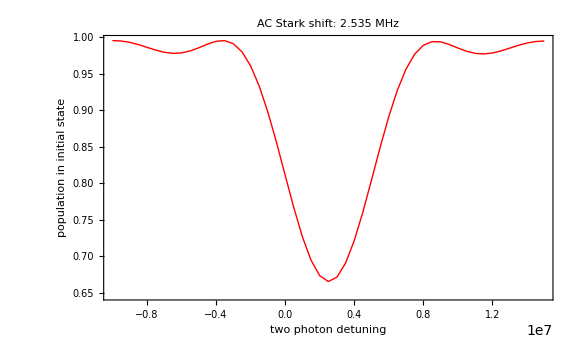

```mathematica
ListPlot[tableTEST,ImageSize->Large,FrameLabel->{"two photon detuning","population in initial state"},FrameTicks->Automatic,ImageSize->500,PlotLabel->"AC Stark shift: 2.535 MHz"]
```